Regular False Method Function Called for f(x)=-2+ⅇ^x_+3 x_-x_^2 for Interval a= 0. and b= 1.

Condition Exists at 4.

# | a | b | c
0 | 0. | 1. | Null
1 | 0. | 1. | 0.2689414213699952
2 | 0. | 0.2689414213699952 | 0.2578356014587604
3 | 0. | 0.2578356014587604 | 0.2575384907116824
4 | 0. | 0.2575384907116824 | 0.2575305059798508

Root x= 0.2575305059798508

Through Built In Routines: {x→0.25753}

Regular False Method Function Called for f(x)=2 Cos[2 x_] x_-(1+x_)^2 for Interval a= -3. and b= -2.

Condition Exists at 8.

# | a | b | c
0 | -3. | -2. | Null
1 | -3. | -2. | -2.141933174718177
2 | -3. | -2.141933174718177 | -2.181835696695272
3 | -3. | -2.181835696695272 | -2.189664227938084
4 | -3. | -2.189664227938084 | -2.191028648970098
5 | -3. | -2.191028648970098 | -2.191260708265559
6 | -3. | -2.191260708265559 | -2.191300007080061
7 | -3. | -2.191300007080061 | -2.1913066573807
8 | -3. | -2.1913066573807 | -2.191307782630977

Root x= -2.191307782630977

Through Built In Routines: {x→-2.19131}

Regular False Method Function Called for f(x)=2 Cos[2 x_] x_-(1+x_)^2 for Interval a= -1. and b= 0.

Condition Exists at 7.

# | a | b | c
0 | -1. | 0. | Null
1 | -1. | 0. | -0.5457640413674794
2 | -1. | -0.5457640413674794 | -0.7548200743265998
3 | -1. | -0.7548200743265998 | -0.7927619936592847
4 | -1. | -0.7927619936592847 | -0.7975294122316235
5 | -1. | -0.7975294122316235 | -0.798086909287865
6 | -1. | -0.798086909287865 | -0.7981515061361502
7 | -1. | -0.7981515061361502 | -0.7981589828771938

Root x= -0.7981589828771938

Through Built In Routines: {x→-0.79816}

Regular False Method Function Called for f(x)=-1+3 x_+Cos[x_] x_-2 x_^2 for Interval a= 0.2 and b= 0.3

Condition Exists at 3.

# | a | b | c
0 | 0.2 | 0.3 | Null
1 | 0.2 | 0.3 | 0.2977284144162926
2 | 0.2 | 0.2977284144162926 | 0.297546099493626
3 | 0.2 | 0.297546099493626 | 0.2975315036115462

Root x= 0.2975315036115462

Through Built In Routines: {x→0.29753}

Regular False Method Function Called for f(x)=-1+3 x_+Cos[x_] x_-2 x_^2 for Interval a= 1.2 and b= 1.3

Condition Exists at 4.

# | a | b | c
0 | 1.2 | 1.3 | Null
1 | 1.2 | 1.3 | 1.253932304140384
2 | 1.253932304140384 | 1.3 | 1.256502654496905
3 | 1.256502654496905 | 1.3 | 1.256617926196684
4 | 1.256617926196684 | 1.3 | 1.256623081210185

Root x= 1.256623081210185

Through Built In Routines: {x→1.25662}

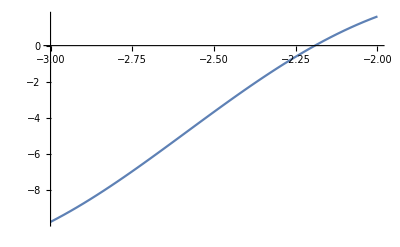
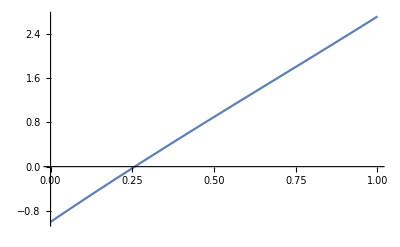
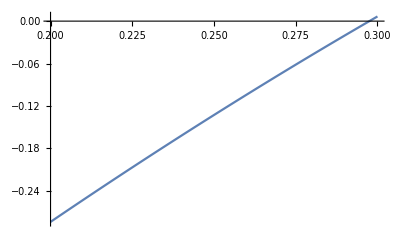
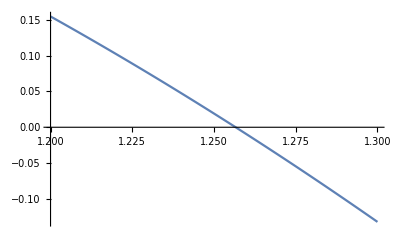
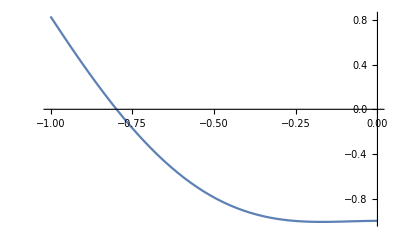
{{Null^14 -Graphics- -Graphics- -Graphics- -Graphics- -Graphics-},{□}}

```mathematica
(*              Aisha Muhammad Nawaz        L20-0921        BSCS SECTION 5E         Assignment #2         Numerical Computing*)

(*Making a function*)
{{regularFalseMethod[a0_,b0_,err_,n_]:=
Module[{},
a=N[a0]; (*First value of Interval*)
b=N[b0]; (*Second value of Interval*)
e=N[err];

i=0;
Print ["Regular False Method Function Called for f(x)=",f[x_]," for Interval a= ",a," and b= ",b];

output={{i,a,b, }};
While [i<n,
c=b-f[b]*(b-a) / (f[b]-f[a]);
output=Append[output,{i+1,a,b,c}];
If[Sign[f[b]]==Sign[f[c]],b=c,a=c];
If[Abs[f[c]]<e,Print["Condition Exists at ", i+1, "."];Break[]];
i=i+1;
];
Print[NumberForm[TableForm[output,TableHeadings->{None,{"#","a","b","c"}}],16]];
Print["Root x= ",NumberForm[c,16]];
]




                                                                          (* TEST PROBLEM #1 *)
f[x_]:=Exp[x]-x^2+3x-2    (*Defining f(x)*)
regularFalseMethod[0,1,10^-5,20] (*Calling the function regularFalse Method*)
Print["Through Built In Routines: ",FindRoot[f[x],{x,0,1}]]; (*Finding root through Built in Function*)
Plot[f[x],{x,0,1} ](*Plotting f(x) in given interval*)

                                                                            (* TEST PROBLEM #2 *)
f[x_]:=2x* Cos[2x]-(x+1)^2    

                                                          (*For interval -3≤x≤-2 *)
regularFalseMethod[-3,-2,10^-5,20] 
Print["Through Built In Routines: ",FindRoot[f[x],{x,-3,-2}]];
Plot[f[x],{x,-3,-2} ]

                                                        (*For interval -1≤x≤0 *)
regularFalseMethod[-1,0,10^-5,20] 
Print["Through Built In Routines: ",FindRoot[f[x],{x,-1,0}]];
Plot[f[x],{x,-1,0} ]

                                                                             (* TEST PROBLEM #3 *)
f[x_]:=x*Cos[x]-2x^2+3x-1   

                                                           (*For interval 0.2≤x≤0.3 *)
regularFalseMethod[0.2,0.3,10^-5,20] 
Print["Through Built In Routines: ",FindRoot[f[x],{x,0.2,0.3}]];
Plot[f[x],{x,0.2,0.3} ]

                                                           (*For interval 1.2≤x≤1.3 *)
regularFalseMethod[1.2,1.3,10^-5,20] 
Print["Through Built In Routines: ",FindRoot[f[x],{x,1.2,1.3}]];
Plot[f[x],{x,1.2,1.3} ]}, {□}}
```